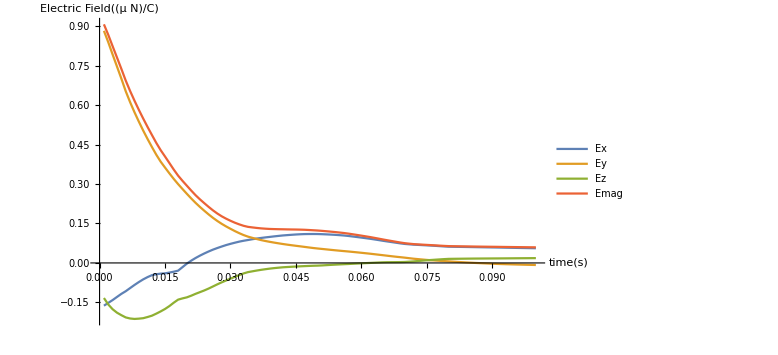

-Graphics3D-

```mathematica
(*
Written by K.Roos
Department of Mechanical Engineering
Bradley University

NOTE:This implementation of the Charges in a Cubic Conductor
(originally produced by Larry Engelhardt in python) contains the basic
structure for calculating the dynamical motion of charges that interact
via the Coulomb interation, using a typical Molecular Dynamics pair
potential approach. It does not attempt to animate the motion of the
charges during the calculation (although there are several ways to accomplish this in Mathematica),but only plots the final position of the
charges (including an image of the cubic conductor)
in a 3D scatter plot after the program has looped through the
specified number of time steps.
*)
ClearAll["Global`*"]

(*set physical parameter values*)
ncharges=100; (*number of individual charges*)
Q=5.0×10^-6; (*net charge in Coulombs*)
m=1.0×10^-3; (*mass of each charge in kg*) 
L=0.2; (*side length of conducting cube in meters*) 
k=8.99×10^9; (*Coulomb constant*) 
qi=Q/ncharges; (*charge on each individual charge*)

(* Coordinates of field point P-- Electric field components due
 to all the charges will be calculated at this point*)
Px=-0.05;
Py=0.043;
Pz=-0.01;

(*algorithmic parameters*)
Δt=0.001; (*time step in seconds*)
tsteps=100; (*total number of time steps*)

(*create charges at random initial positions (all initially at rest)*)
For[i=1,i≤ncharges,i++,
x[i]=(-1)^IntegerPart[2*RandomReal[]]*L/2*RandomReal[];
y[i]=(-1)^IntegerPart[2*RandomReal[]]*L/2*RandomReal[];
z[i]=(-1)^IntegerPart[2*RandomReal[]]*L/2*RandomReal[];
vx[i]=0;
vy[i]=0;
vz[i]=0;
]
(*Initialize electric field components for each time step to zero*)
For[n=1,n≤tsteps,n++,
Ex[n]=0;
Ey[n]=0;
Ez[n]=0;
]
(*Main loop*)
For[n=1,n≤tsteps,n++,
time[n]=n*Δt;
(* reset net force in x,y,z directions to zero for all charges *)
   For[i=1,i≤ncharges,i++,
fx[i]=0;
fy[i]=0;
fz[i]=0;
]
(*Calculate forces on each pair of charges by considering
i-j pairs.% The structure of the nested for loops prevents double counting of
    pairs*)
For[i=1,i≤ncharges-1,i++,
For[j=i+1,j≤ncharges,j++,
dx=x[i]-x[j];
	dy=y[i]-y[j];
	dz=z[i]-z[j];
	rmag=Sqrt[dx*dx+dy*dy+dz*dz];
(*Magnitude of mutual Coulomb force between charges i and j*)
	fij=k*qi*qi/(rmag*rmag);
(*The three spatial components of the force between charges
i and j*)	
fijx=fij*dx/rmag;
	fijy=fij*dy/rmag;
	fijz=fij*dz/rmag;
(*Accumulation of the components of the net force acting on
     charges i and j*)
	fx[i]+=fijx;
	fy[i]+=fijy;
	fz[i]+=fijz;
	fx[j]+=-fijx;
	fy[j]+=-fijy;
	fz[j]+=-fijz;
]
]
(* positions updated for all charges 
For the algorithm for updating positions, use the large friction
   limit wherein the force is replaced by displacement. This approach
   is the simplest stable algorithm for this geometry; thus, this
simulation emphasizes the resultant configuration of excess charge
   after equilibration, rather than the correct physics governing the
   dynamical motion of the system.*)
For[i=1,i≤ncharges,i++,
(* With force representing displacement, rescale displacement
    in the case of a large calculated displacement *)
         magf=Sqrt[fx[i]*fx[i]+fy[i]*fy[i]+fz[i]*fz[i]];
   If[magf>L/100, 
fx[i]=(L/100)*fx[i]/magf;
fy[i]=(L/100)*fy[i]/magf;
fz[i]=(L/100)*fz[i]/magf;
];
(* update positions with large friction approximation*)
       x[i]+=fx[i]; 
	     y[i]+=fy[i];
	     z[i]+=fz[i];
(* if charge moved beyond surface of conductor,bring it back to surface *)
If[x[i]>L/2,x[i]=L/2];
If[x[i]<-L/2,x[i]=-L/2];
If[y[i]>L/2,y[i]=L/2];
If[y[i]<-L/2,y[i]=-L/2];
If[z[i]>L/2,z[i]=L/2];
If[z[i]<-L/2,z[i]=-L/2];
(* Calculation of Electric Field components at point P*)
(*----------------------------------------------------------------

 THE CALCULATION OF THE ELECTRIC FIELD COMPONENTS AND MAGNITUDE
 GOES HERE

----------------------------------------------------------------*)
]
] (* end of main loop *)
(*Plotting commands*)
tx=Table[{time[i],Ex[i]},{i,1,tsteps}];
ty=Table[{time[i],Ey[i]},{i,1,tsteps}];
tz=Table[{time[i],Ez[i]},{i,1,tsteps}];
tmag=Table[{time[i],Emag[i]},{i,1,tsteps}];
ListLinePlot[{tx,ty,tz,tmag},ImageSize-> Large,PlotRange->All,AxesLabel->{HoldForm[time[s]],HoldForm[Electric Field [μ N/C]]},PlotLabel->None,PlotLegends->{"Ex","Ey","Ez","Emag"},LabelStyle->{FontFamily->"Arial",18,GrayLevel[0]}]
plot=Table[{x[i],y[i],z[i]},{i,1,ncharges}];
Graphics3D[{Opacity[0.5],{Glow[LightBlue],Black,Cuboid[{-L/2,-L/2,-L/2},{L/2,L/2,L/2}]},Red,PointSize[0.015],Point[plot],PlotMarkers->{"Sphere",Large},Axes->True,BoxRatios->1,Boxed->False},ImageSize->Large,PlotRange->{{-L/2,L/2},{-L/2,L/2},{-L/2,L/2}},Lighting->Automatic]
```